```mathematica
LinguisticAssistant
```

```mathematica
f[t_] := ((Cos[t] - Cos[end]) / (Cos[start] - Cos[end]))^4 Sin[t]
```

```mathematica
Integrate[f[t], {t, start, end}]
```

1/5 (-Cos[end]+Cos[start])

```mathematica
LinguisticAssistant
```

```mathematica
pdf[t_] := f[t] / %2
```

```mathematica
pdf[t]
```

(5 (-Cos[end]+Cos[t])^4 Sin[t])/(-Cos[end]+Cos[start])^5

```mathematica
Integrate[%4, {t,start,end}]
```

1

```mathematica
Integrate[pdf[tp], {tp, start, t}]
```

1/(16 (-Cos[end]+Cos[start])^5)(10 (10+10 Cos[2 end]+Cos[4 end]) Cos[start]-40 Cos[end] Cos[start]^2 (3+2 Cos[2 end]+Cos[2 start])+5 (5+4 Cos[2 end]) Cos[3 start]+Cos[5 start]-10 (10+10 Cos[2 end]+Cos[4 end]) Cos[t]+40 Cos[end] Cos[t]^2 (3+2 Cos[2 end]+Cos[2 t])-5 (5+4 Cos[2 end]) Cos[3 t]-Cos[5 t])

```mathematica
cdf[t_] := Integrate[pdf[tp], {tp, start, t}]
```

```mathematica
cdf[t]
```

(10 (10+10 Cos[2 end]+Cos[4 end]) Cos[start]-40 Cos[end] Cos[start]^2 (3+2 Cos[2 end]+Cos[2 start])+5 (5+4 Cos[2 end]) Cos[3 start]+Cos[5 start]-10 (10+10 Cos[2 end]+Cos[4 end]) Cos[t]+40 Cos[end] Cos[t]^2 (3+2 Cos[2 end]+Cos[2 t])-5 (5+4 Cos[2 end]) Cos[3 t]-Cos[5 t])/(16 (-Cos[end]+Cos[start])^5)

```mathematica
Integrate[%4, {t, start,end}]
```

1

```mathematica
Collect[%6, t]
```

1/(16 (-Cos[end]+Cos[start])^5)(10 (10+10 Cos[2 end]+Cos[4 end]) Cos[start]-40 Cos[end] Cos[start]^2 (3+2 Cos[2 end]+Cos[2 start])+5 (5+4 Cos[2 end]) Cos[3 start]+Cos[5 start]-10 (10+10 Cos[2 end]+Cos[4 end]) Cos[t]+40 Cos[end] Cos[t]^2 (3+2 Cos[2 end]+Cos[2 t])-5 (5+4 Cos[2 end]) Cos[3 t]-Cos[5 t])

```mathematica
Simplify[%20]
```

1/(16 (-Cos[end]+Cos[start])^5)(10 (10+10 Cos[2 end]+Cos[4 end]) Cos[start]-40 Cos[end] Cos[start]^2 (3+2 Cos[2 end]+Cos[2 start])+5 (5+4 Cos[2 end]) Cos[3 start]+Cos[5 start]-10 (10+10 Cos[2 end]+Cos[4 end]) Cos[t]+40 Cos[end] Cos[t]^2 (3+2 Cos[2 end]+Cos[2 t])-5 (5+4 Cos[2 end]) Cos[3 t]-Cos[5 t])

```mathematica
TrigExpand[%22]
```

(25 Cos[start])/(4 (-Cos[end]+Cos[start])^5)+(25 Cos[end]^2 Cos[start])/(4 (-Cos[end]+Cos[start])^5)+(5 Cos[end]^4 Cos[start])/(8 (-Cos[end]+Cos[start])^5)-(25 Cos[end] Cos[start]^2)/(4 (-Cos[end]+Cos[start])^5)-(5 Cos[end]^3 Cos[start]^2)/(4 (-Cos[end]+Cos[start])^5)+(25 Cos[start]^3)/(16 (-Cos[end]+Cos[start])^5)+(5 Cos[end]^2 Cos[start]^3)/(4 (-Cos[end]+Cos[start])^5)-(5 Cos[end] Cos[start]^4)/(8 (-Cos[end]+Cos[start])^5)+Cos[start]^5/(16 (-Cos[end]+Cos[start])^5)-(25 Cos[t])/(4 (-Cos[end]+Cos[start])^5)-(25 Cos[end]^2 Cos[t])/(4 (-Cos[end]+Cos[start])^5)-(5 Cos[end]^4 Cos[t])/(8 (-Cos[end]+Cos[start])^5)+(25 Cos[end] Cos[t]^2)/(4 (-Cos[end]+Cos[start])^5)+(5 Cos[end]^3 Cos[t]^2)/(4 (-Cos[end]+Cos[start])^5)-(25 Cos[t]^3)/(16 (-Cos[end]+Cos[start])^5)-(5 Cos[end]^2 Cos[t]^3)/(4 (-Cos[end]+Cos[start])^5)+(5 Cos[end] Cos[t]^4)/(8 (-Cos[end]+Cos[start])^5)-Cos[t]^5/(16 (-Cos[end]+Cos[start])^5)-(25 Cos[start] Sin[end]^2)/(4 (-Cos[end]+Cos[start])^5)-(15 Cos[end]^2 Cos[start] Sin[end]^2)/(4 (-Cos[end]+Cos[start])^5)+(15 Cos[end] Cos[start]^2 Sin[end]^2)/(4 (-Cos[end]+Cos[start])^5)-(5 Cos[start]^3 Sin[end]^2)/(4 (-Cos[end]+Cos[start])^5)+(25 Cos[t] Sin[end]^2)/(4 (-Cos[end]+Cos[start])^5)+(15 Cos[end]^2 Cos[t] Sin[end]^2)/(4 (-Cos[end]+Cos[start])^5)-(15 Cos[end] Cos[t]^2 Sin[end]^2)/(4 (-Cos[end]+Cos[start])^5)+(5 Cos[t]^3 Sin[end]^2)/(4 (-Cos[end]+Cos[start])^5)+(5 Cos[start] Sin[end]^4)/(8 (-Cos[end]+Cos[start])^5)-(5 Cos[t] Sin[end]^4)/(8 (-Cos[end]+Cos[start])^5)+(25 Cos[end] Sin[start]^2)/(4 (-Cos[end]+Cos[start])^5)+(5 Cos[end]^3 Sin[start]^2)/(4 (-Cos[end]+Cos[start])^5)-(75 Cos[start] Sin[start]^2)/(16 (-Cos[end]+Cos[start])^5)-(15 Cos[end]^2 Cos[start] Sin[start]^2)/(4 (-Cos[end]+Cos[start])^5)+(15 Cos[end] Cos[start]^2 Sin[start]^2)/(4 (-Cos[end]+Cos[start])^5)-(5 Cos[start]^3 Sin[start]^2)/(8 (-Cos[end]+Cos[start])^5)-(15 Cos[end] Sin[end]^2 Sin[start]^2)/(4 (-Cos[end]+Cos[start])^5)+(15 Cos[start] Sin[end]^2 Sin[start]^2)/(4 (-Cos[end]+Cos[start])^5)-(5 Cos[end] Sin[start]^4)/(8 (-Cos[end]+Cos[start])^5)+(5 Cos[start] Sin[start]^4)/(16 (-Cos[end]+Cos[start])^5)-(25 Cos[end] Sin[t]^2)/(4 (-Cos[end]+Cos[start])^5)-(5 Cos[end]^3 Sin[t]^2)/(4 (-Cos[end]+Cos[start])^5)+(75 Cos[t] Sin[t]^2)/(16 (-Cos[end]+Cos[start])^5)+(15 Cos[end]^2 Cos[t] Sin[t]^2)/(4 (-Cos[end]+Cos[start])^5)-(15 Cos[end] Cos[t]^2 Sin[t]^2)/(4 (-Cos[end]+Cos[start])^5)+(5 Cos[t]^3 Sin[t]^2)/(8 (-Cos[end]+Cos[start])^5)+(15 Cos[end] Sin[end]^2 Sin[t]^2)/(4 (-Cos[end]+Cos[start])^5)-(15 Cos[t] Sin[end]^2 Sin[t]^2)/(4 (-Cos[end]+Cos[start])^5)+(5 Cos[end] Sin[t]^4)/(8 (-Cos[end]+Cos[start])^5)-(5 Cos[t] Sin[t]^4)/(16 (-Cos[end]+Cos[start])^5)

```mathematica
% /. {Sin[t]^2 -> 1 - Cos[t]^2, Sin[t]^4 -> (1 - Cos[t]^2)^2}
```

(25 Cos[start])/(4 (-Cos[end]+Cos[start])^5)+(25 Cos[end]^2 Cos[start])/(4 (-Cos[end]+Cos[start])^5)+(5 Cos[end]^4 Cos[start])/(8 (-Cos[end]+Cos[start])^5)-(25 Cos[end] Cos[start]^2)/(4 (-Cos[end]+Cos[start])^5)-(5 Cos[end]^3 Cos[start]^2)/(4 (-Cos[end]+Cos[start])^5)+(25 Cos[start]^3)/(16 (-Cos[end]+Cos[start])^5)+(5 Cos[end]^2 Cos[start]^3)/(4 (-Cos[end]+Cos[start])^5)-(5 Cos[end] Cos[start]^4)/(8 (-Cos[end]+Cos[start])^5)+Cos[start]^5/(16 (-Cos[end]+Cos[start])^5)-(25 Cos[t])/(4 (-Cos[end]+Cos[start])^5)-(25 Cos[end]^2 Cos[t])/(4 (-Cos[end]+Cos[start])^5)-(5 Cos[end]^4 Cos[t])/(8 (-Cos[end]+Cos[start])^5)+(25 Cos[end] Cos[t]^2)/(4 (-Cos[end]+Cos[start])^5)+(5 Cos[end]^3 Cos[t]^2)/(4 (-Cos[end]+Cos[start])^5)-(25 Cos[t]^3)/(16 (-Cos[end]+Cos[start])^5)-(5 Cos[end]^2 Cos[t]^3)/(4 (-Cos[end]+Cos[start])^5)+(5 Cos[end] Cos[t]^4)/(8 (-Cos[end]+Cos[start])^5)-Cos[t]^5/(16 (-Cos[end]+Cos[start])^5)-(25 Cos[end] (1-Cos[t]^2))/(4 (-Cos[end]+Cos[start])^5)-(5 Cos[end]^3 (1-Cos[t]^2))/(4 (-Cos[end]+Cos[start])^5)+(75 Cos[t] (1-Cos[t]^2))/(16 (-Cos[end]+Cos[start])^5)+(15 Cos[end]^2 Cos[t] (1-Cos[t]^2))/(4 (-Cos[end]+Cos[start])^5)-(15 Cos[end] Cos[t]^2 (1-Cos[t]^2))/(4 (-Cos[end]+Cos[start])^5)+(5 Cos[t]^3 (1-Cos[t]^2))/(8 (-Cos[end]+Cos[start])^5)+(5 Cos[end] (1-Cos[t]^2)^2)/(8 (-Cos[end]+Cos[start])^5)-(5 Cos[t] (1-Cos[t]^2)^2)/(16 (-Cos[end]+Cos[start])^5)-(25 Cos[start] Sin[end]^2)/(4 (-Cos[end]+Cos[start])^5)-(15 Cos[end]^2 Cos[start] Sin[end]^2)/(4 (-Cos[end]+Cos[start])^5)+(15 Cos[end] Cos[start]^2 Sin[end]^2)/(4 (-Cos[end]+Cos[start])^5)-(5 Cos[start]^3 Sin[end]^2)/(4 (-Cos[end]+Cos[start])^5)+(25 Cos[t] Sin[end]^2)/(4 (-Cos[end]+Cos[start])^5)+(15 Cos[end]^2 Cos[t] Sin[end]^2)/(4 (-Cos[end]+Cos[start])^5)-(15 Cos[end] Cos[t]^2 Sin[end]^2)/(4 (-Cos[end]+Cos[start])^5)+(5 Cos[t]^3 Sin[end]^2)/(4 (-Cos[end]+Cos[start])^5)+(15 Cos[end] (1-Cos[t]^2) Sin[end]^2)/(4 (-Cos[end]+Cos[start])^5)-(15 Cos[t] (1-Cos[t]^2) Sin[end]^2)/(4 (-Cos[end]+Cos[start])^5)+(5 Cos[start] Sin[end]^4)/(8 (-Cos[end]+Cos[start])^5)-(5 Cos[t] Sin[end]^4)/(8 (-Cos[end]+Cos[start])^5)+(25 Cos[end] Sin[start]^2)/(4 (-Cos[end]+Cos[start])^5)+(5 Cos[end]^3 Sin[start]^2)/(4 (-Cos[end]+Cos[start])^5)-(75 Cos[start] Sin[start]^2)/(16 (-Cos[end]+Cos[start])^5)-(15 Cos[end]^2 Cos[start] Sin[start]^2)/(4 (-Cos[end]+Cos[start])^5)+(15 Cos[end] Cos[start]^2 Sin[start]^2)/(4 (-Cos[end]+Cos[start])^5)-(5 Cos[start]^3 Sin[start]^2)/(8 (-Cos[end]+Cos[start])^5)-(15 Cos[end] Sin[end]^2 Sin[start]^2)/(4 (-Cos[end]+Cos[start])^5)+(15 Cos[start] Sin[end]^2 Sin[start]^2)/(4 (-Cos[end]+Cos[start])^5)-(5 Cos[end] Sin[start]^4)/(8 (-Cos[end]+Cos[start])^5)+(5 Cos[start] Sin[start]^4)/(16 (-Cos[end]+Cos[start])^5)

```mathematica
Simplify[%]
```

1/(16 (Cos[end]-Cos[start])^5)(-Cos[start]^5-5 Cos[start]^3 (2+2 Cos[2 end]+Cos[2 start])-5/8 Cos[start] (111+120 Cos[2 end]+16 Cos[4 end]+28 Cos[2 (end-start)]+64 Cos[2 start]+Cos[4 start]+28 Cos[2 (end+start)])+10 Cos[end]^4 Cos[t]-80 Cos[end]^2 Cos[start]^2 Cos[t]+16 Cos[t]^5+20 Cos[end]^3 (Cos[2 start]-Cos[2 t])+10 Cos[end] (Cos[2 start]-Cos[2 t]) (7+3 Cos[2 end]+2 Cos[2 start]+2 Cos[2 t])+5 Cos[end]^2 Cos[t] (31+7 Cos[2 end]+8 Cos[2 start]+16 Cos[2 t]))

```mathematica
%29/. {Cos[2t]-> 2 Cos[t]^2-1}
```

1/(16 (Cos[end]-Cos[start])^5)(-Cos[start]^5-5 Cos[start]^3 (2+2 Cos[2 end]+Cos[2 start])-5/8 Cos[start] (111+120 Cos[2 end]+16 Cos[4 end]+28 Cos[2 (end-start)]+64 Cos[2 start]+Cos[4 start]+28 Cos[2 (end+start)])+10 Cos[end]^4 Cos[t]-80 Cos[end]^2 Cos[start]^2 Cos[t]+16 Cos[t]^5+20 Cos[end]^3 (1+Cos[2 start]-2 Cos[t]^2)+10 Cos[end] (1+Cos[2 start]-2 Cos[t]^2) (7+3 Cos[2 end]+2 Cos[2 start]+2 (-1+2 Cos[t]^2))+5 Cos[end]^2 Cos[t] (31+7 Cos[2 end]+8 Cos[2 start]+16 (-1+2 Cos[t]^2)))

```mathematica
Collect[%, Cos[t]]
```

1/(16 (Cos[end]-Cos[start])^5)(50 Cos[end]+20 Cos[end]^3+30 Cos[end] Cos[2 end]-Cos[start]^5+70 Cos[end] Cos[2 start]+20 Cos[end]^3 Cos[2 start]+30 Cos[end] Cos[2 end] Cos[2 start]+20 Cos[end] Cos[2 start]^2-5 Cos[start]^3 (2+2 Cos[2 end]+Cos[2 start])-5/8 Cos[start] (111+120 Cos[2 end]+16 Cos[4 end]+28 Cos[2 (end-start)]+64 Cos[2 start]+Cos[4 start]+28 Cos[2 (end+start)]))+((75 Cos[end]^2+10 Cos[end]^4+35 Cos[end]^2 Cos[2 end]-80 Cos[end]^2 Cos[start]^2+40 Cos[end]^2 Cos[2 start]) Cos[t])/(16 (Cos[end]-Cos[start])^5)+((-60 Cos[end]-40 Cos[end]^3-60 Cos[end] Cos[2 end]) Cos[t]^2)/(16 (Cos[end]-Cos[start])^5)+(10 Cos[end]^2 Cos[t]^3)/(Cos[end]-Cos[start])^5-(5 Cos[end] Cos[t]^4)/(Cos[end]-Cos[start])^5+Cos[t]^5/(Cos[end]-Cos[start])^5

```mathematica
%36 /. {Cos[2 start] -> 2 Cos[start]^2 - 1, Cos[2 end] -> 2 Cos[end]^2 - 1}
```

1/(16 (Cos[end]-Cos[start])^5)(50 Cos[end]+20 Cos[end]^3+30 Cos[end] (-1+2 Cos[end]^2)-Cos[start]^5+70 Cos[end] (-1+2 Cos[start]^2)+20 Cos[end]^3 (-1+2 Cos[start]^2)+30 Cos[end] (-1+2 Cos[end]^2) (-1+2 Cos[start]^2)+20 Cos[end] (-1+2 Cos[start]^2)^2-5 Cos[start]^3 (1+2 (-1+2 Cos[end]^2)+2 Cos[start]^2)-5/8 Cos[start] (111+120 (-1+2 Cos[end]^2)+16 Cos[4 end]+28 Cos[2 (end-start)]+64 (-1+2 Cos[start]^2)+Cos[4 start]+28 Cos[2 (end+start)]))+((75 Cos[end]^2+10 Cos[end]^4+35 Cos[end]^2 (-1+2 Cos[end]^2)-80 Cos[end]^2 Cos[start]^2+40 Cos[end]^2 (-1+2 Cos[start]^2)) Cos[t])/(16 (Cos[end]-Cos[start])^5)+((-60 Cos[end]-40 Cos[end]^3-60 Cos[end] (-1+2 Cos[end]^2)) Cos[t]^2)/(16 (Cos[end]-Cos[start])^5)+(10 Cos[end]^2 Cos[t]^3)/(Cos[end]-Cos[start])^5-(5 Cos[end] Cos[t]^4)/(Cos[end]-Cos[start])^5+Cos[t]^5/(Cos[end]-Cos[start])^5

```mathematica
% /. {Cos[2(end-start)] -> Cos[2end]Cos[2start]+Sin[2end]Sin[2start], Cos[2(end+start)] -> Cos[2end]Cos[2start]-Sin[2end]Sin[2start]}
```

((75 Cos[end]^2+10 Cos[end]^4+35 Cos[end]^2 (-1+2 Cos[end]^2)-80 Cos[end]^2 Cos[start]^2+40 Cos[end]^2 (-1+2 Cos[start]^2)) Cos[t])/(16 (Cos[end]-Cos[start])^5)+((-60 Cos[end]-40 Cos[end]^3-60 Cos[end] (-1+2 Cos[end]^2)) Cos[t]^2)/(16 (Cos[end]-Cos[start])^5)+(10 Cos[end]^2 Cos[t]^3)/(Cos[end]-Cos[start])^5-(5 Cos[end] Cos[t]^4)/(Cos[end]-Cos[start])^5+Cos[t]^5/(Cos[end]-Cos[start])^5+1/(16 (Cos[end]-Cos[start])^5)(50 Cos[end]+20 Cos[end]^3+30 Cos[end] (-1+2 Cos[end]^2)-Cos[start]^5+70 Cos[end] (-1+2 Cos[start]^2)+20 Cos[end]^3 (-1+2 Cos[start]^2)+30 Cos[end] (-1+2 Cos[end]^2) (-1+2 Cos[start]^2)+20 Cos[end] (-1+2 Cos[start]^2)^2-5 Cos[start]^3 (1+2 (-1+2 Cos[end]^2)+2 Cos[start]^2)-5/8 Cos[start] (111+120 (-1+2 Cos[end]^2)+16 Cos[4 end]+64 (-1+2 Cos[start]^2)+Cos[4 start]+28 (Cos[2 end] Cos[2 start]-Sin[2 end] Sin[2 start])+28 (Cos[2 end] Cos[2 start]+Sin[2 end] Sin[2 start])))

```mathematica
% /. {Sin[2end]->2 Sqrt[1 - Cos[end]^2]Cos[end], Sin[2start]->2 Sqrt[1 - Cos[start]^2]Cos[start]}
```

1/(16 (Cos[end]-Cos[start])^5)(50 Cos[end]+20 Cos[end]^3+30 Cos[end] (-1+2 Cos[end]^2)-Cos[start]^5+70 Cos[end] (-1+2 Cos[start]^2)+20 Cos[end]^3 (-1+2 Cos[start]^2)+30 Cos[end] (-1+2 Cos[end]^2) (-1+2 Cos[start]^2)+20 Cos[end] (-1+2 Cos[start]^2)^2-5 Cos[start]^3 (1+2 (-1+2 Cos[end]^2)+2 Cos[start]^2)-5/8 Cos[start] (111+120 (-1+2 Cos[end]^2)+16 Cos[4 end]+64 (-1+2 Cos[start]^2)+28 (-4 Cos[end] √(1-Cos[end]^2) Cos[start] √(1-Cos[start]^2)+Cos[2 end] Cos[2 start])+28 (4 Cos[end] √(1-Cos[end]^2) Cos[start] √(1-Cos[start]^2)+Cos[2 end] Cos[2 start])+Cos[4 start]))+((75 Cos[end]^2+10 Cos[end]^4+35 Cos[end]^2 (-1+2 Cos[end]^2)-80 Cos[end]^2 Cos[start]^2+40 Cos[end]^2 (-1+2 Cos[start]^2)) Cos[t])/(16 (Cos[end]-Cos[start])^5)+((-60 Cos[end]-40 Cos[end]^3-60 Cos[end] (-1+2 Cos[end]^2)) Cos[t]^2)/(16 (Cos[end]-Cos[start])^5)+(10 Cos[end]^2 Cos[t]^3)/(Cos[end]-Cos[start])^5-(5 Cos[end] Cos[t]^4)/(Cos[end]-Cos[start])^5+Cos[t]^5/(Cos[end]-Cos[start])^5

```mathematica
Simplify[%, start ≥ 0 && start < Pi/2 && end ≥ 0 && end < Pi/2]
```

1/(128 (Cos[end]-Cos[start])^5)(1280 Cos[end]^3 Cos[start]^2-40 (17+2 Cos[2 end]) Cos[start]^3+640 Cos[end] Cos[start]^4-88 Cos[start]^5-5 Cos[start] (-73+240 Cos[end]^2+16 Cos[4 end]+56 Cos[2 end] Cos[2 start]+Cos[4 start])+128 Cos[t] (5 Cos[end]^4-10 Cos[end]^3 Cos[t]+10 Cos[end]^2 Cos[t]^2-5 Cos[end] Cos[t]^3+Cos[t]^4))

```mathematica
LinguisticAssistant
```

```mathematica
Collect[%, Cos[t]]
```

1/(128 (Cos[end]-Cos[start])^5)(1280 Cos[end]^3 Cos[start]^2-40 (17+2 Cos[2 end]) Cos[start]^3+640 Cos[end] Cos[start]^4-88 Cos[start]^5-5 Cos[start] (-73+240 Cos[end]^2+16 Cos[4 end]+56 Cos[2 end] Cos[2 start]+Cos[4 start]))+(5 Cos[end]^4 Cos[t])/(Cos[end]-Cos[start])^5-(10 Cos[end]^3 Cos[t]^2)/(Cos[end]-Cos[start])^5+(10 Cos[end]^2 Cos[t]^3)/(Cos[end]-Cos[start])^5-(5 Cos[end] Cos[t]^4)/(Cos[end]-Cos[start])^5+Cos[t]^5/(Cos[end]-Cos[start])^5

```mathematica
%43 /. {Cos[4 start] -> 2 Cos[2 start]^2 - 1, Cos[4 end] -> 2 Cos[2 end]^2 - 1}
```

1/(128 (Cos[end]-Cos[start])^5)(1280 Cos[end]^3 Cos[start]^2-40 (17+2 Cos[2 end]) Cos[start]^3+640 Cos[end] Cos[start]^4-88 Cos[start]^5-5 Cos[start] (-74+240 Cos[end]^2+16 (-1+2 Cos[2 end]^2)+56 Cos[2 end] Cos[2 start]+2 Cos[2 start]^2))+(5 Cos[end]^4 Cos[t])/(Cos[end]-Cos[start])^5-(10 Cos[end]^3 Cos[t]^2)/(Cos[end]-Cos[start])^5+(10 Cos[end]^2 Cos[t]^3)/(Cos[end]-Cos[start])^5-(5 Cos[end] Cos[t]^4)/(Cos[end]-Cos[start])^5+Cos[t]^5/(Cos[end]-Cos[start])^5

```mathematica
%50 /. {Cos[2 start] -> 2 Cos[start]^2 - 1, Cos[2 end] -> 2 Cos[end]^2 - 1}
```

1/(128 (Cos[end]-Cos[start])^5)(1280 Cos[end]^3 Cos[start]^2-40 (17+2 (-1+2 Cos[end]^2)) Cos[start]^3+640 Cos[end] Cos[start]^4-88 Cos[start]^5-5 Cos[start] (-74+240 Cos[end]^2+16 (-1+2 (-1+2 Cos[end]^2)^2)+56 (-1+2 Cos[end]^2) (-1+2 Cos[start]^2)+2 (-1+2 Cos[start]^2)^2))+(5 Cos[end]^4 Cos[t])/(Cos[end]-Cos[start])^5-(10 Cos[end]^3 Cos[t]^2)/(Cos[end]-Cos[start])^5+(10 Cos[end]^2 Cos[t]^3)/(Cos[end]-Cos[start])^5-(5 Cos[end] Cos[t]^4)/(Cos[end]-Cos[start])^5+Cos[t]^5/(Cos[end]-Cos[start])^5

```mathematica
Collect[%, Cos[t]]
```

1/(128 (Cos[end]-Cos[start])^5)(1280 Cos[end]^3 Cos[start]^2-40 (17+2 (-1+2 Cos[end]^2)) Cos[start]^3+640 Cos[end] Cos[start]^4-88 Cos[start]^5-5 Cos[start] (-74+240 Cos[end]^2+16 (-1+2 (-1+2 Cos[end]^2)^2)+56 (-1+2 Cos[end]^2) (-1+2 Cos[start]^2)+2 (-1+2 Cos[start]^2)^2))+(5 Cos[end]^4 Cos[t])/(Cos[end]-Cos[start])^5-(10 Cos[end]^3 Cos[t]^2)/(Cos[end]-Cos[start])^5+(10 Cos[end]^2 Cos[t]^3)/(Cos[end]-Cos[start])^5-(5 Cos[end] Cos[t]^4)/(Cos[end]-Cos[start])^5+Cos[t]^5/(Cos[end]-Cos[start])^5

```mathematica
CForm[%52]
```

(1280*Power(Cos(end),3)*Power(Cos(start),2) - 40*(17 + 2*(-1 + 2*Power(Cos(end),2)))*Power(Cos(start),3) + 640*Cos(end)*Power(Cos(start),4) - 
      88*Power(Cos(start),5) - 5*Cos(start)*(-74 + 240*Power(Cos(end),2) + 16*(-1 + 2*Power(-1 + 2*Power(Cos(end),2),2)) + 
         56*(-1 + 2*Power(Cos(end),2))*(-1 + 2*Power(Cos(start),2)) + 2*Power(-1 + 2*Power(Cos(start),2),2)))/(128.*Power(Cos(end) - Cos(start),5)) + 
   (5*Power(Cos(end),4)*Cos(t))/Power(Cos(end) - Cos(start),5) - (10*Power(Cos(end),3)*Power(Cos(t),2))/Power(Cos(end) - Cos(start),5) + 
   (10*Power(Cos(end),2)*Power(Cos(t),3))/Power(Cos(end) - Cos(start),5) - (5*Cos(end)*Power(Cos(t),4))/Power(Cos(end) - Cos(start),5) + 
   Power(Cos(t),5)/Power(Cos(end) - Cos(start),5)

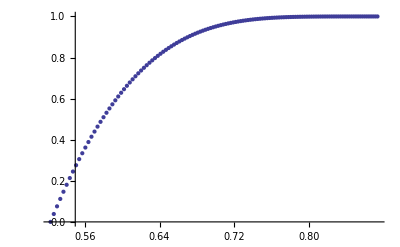

```mathematica
ListPlot[{{0.523599,0.000000},{0.527077,0.038458},{0.530533,0.075721},{0.533970,0.111822},{0.537387,0.146786},{0.540784,0.180639},{0.544163,0.213408},{0.547522,0.245122},{0.550863,0.275803},{0.554186,0.305480},{0.557491,0.334175},{0.560779,0.361914},{0.564050,0.388721},{0.567304,0.414619},{0.570541,0.439630},{0.573762,0.463781},{0.576968,0.487092},{0.580157,0.509583},{0.583331,0.531280},{0.586490,0.552202},{0.589634,0.572370},{0.592763,0.591803},{0.595877,0.610526},{0.598978,0.628553},{0.602064,0.645908},{0.605137,0.662607},{0.608196,0.678671},{0.611241,0.694115},{0.614274,0.708962},{0.617293,0.723226},{0.620300,0.736924},{0.623294,0.750076},{0.626276,0.762696},{0.629245,0.774800},{0.632203,0.786406},{0.635148,0.797528},{0.638082,0.808181},{0.641004,0.818383},{0.643915,0.828145},{0.646814,0.837483},{0.649703,0.846410},{0.652580,0.854940},{0.655447,0.863087},{0.658303,0.870867},{0.661149,0.878285},{0.663984,0.885359},{0.666809,0.892100},{0.669624,0.898522},{0.672429,0.904632},{0.675224,0.910446},{0.678009,0.915972},{0.680785,0.921223},{0.683551,0.926206},{0.686308,0.930936},{0.689055,0.935418},{0.691794,0.939665},{0.694523,0.943685},{0.697244,0.947490},{0.699956,0.951085},{0.702659,0.954481},{0.705353,0.957684},{0.708039,0.960705},{0.710716,0.963552},{0.713386,0.966231},{0.716047,0.968751},{0.718700,0.971116},{0.721345,0.973337},{0.723982,0.975420},{0.726611,0.977369},{0.729232,0.979193},{0.731846,0.980899},{0.734452,0.982489},{0.737051,0.983971},{0.739642,0.985352},{0.742226,0.986638},{0.744802,0.987829},{0.747372,0.988934},{0.749934,0.989960},{0.752489,0.990904},{0.755037,0.991779},{0.757579,0.992585},{0.760114,0.993325},{0.762641,0.994008},{0.765163,0.994631},{0.767677,0.995200},{0.770185,0.995720},{0.772687,0.996195},{0.775182,0.996628},{0.777671,0.997019},{0.780154,0.997376},{0.782630,0.997694},{0.785100,0.997985},{0.787565,0.998240},{0.790023,0.998470},{0.792475,0.998678},{0.794921,0.998863},{0.797361,0.999025},{0.799796,0.999168},{0.802225,0.999294},{0.804648,0.999402},{0.807065,0.999498},{0.809477,0.999582},{0.811884,0.999652},{0.814285,0.999717},{0.816680,0.999769},{0.819070,0.999814},{0.821455,0.999850},{0.823835,0.999881},{0.826209,0.999907},{0.828578,0.999928},{0.830942,0.999944},{0.833301,0.999958},{0.835654,0.999969},{0.838003,0.999980},{0.840347,0.999986},{0.842686,0.999987},{0.845020,0.999991},{0.847349,0.999997},{0.849674,0.999995},{0.851994,1.000000},{0.854309,0.999996},{0.856619,0.999996},{0.858925,0.999997},{0.861226,0.999999},{0.863523,0.999998},{0.865815,0.999996},{0.868102,0.999997},{0.870386,0.999996},{0.872665,0.999996}}]
```

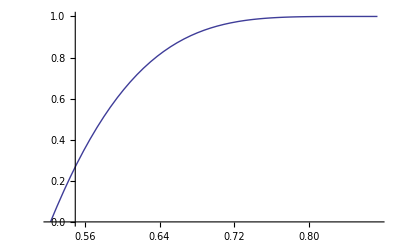

```mathematica
Plot[%52/. {start->30*Pi/180, end->50*Pi/180}, {t,30*Pi/180,50*Pi/180} , PlotRange->Full]
```